```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];(*Get["HopfE`"];*)
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[bev]:=Subscript[β,v];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];Format[si]:=σ;Format[rh]:=ρ;
Format[muv]:=Subscript[μ,v];Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
Format[c1]:=Subscript[c,1];Format[c2]:=Subscript[c,2];
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"->"v","v"+"i2"->2"i2","s"->0,"v"->0,"i1"->0,"i2"->0};

rts={La,be1*s*i1,be2*s*i2,rh *s,bev*v*i2,mu*s,muv*v,(mu1)*i1,(mu2)*i2};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,ngm}= bdAn[RN,rts];
RHS
mod={RHS,var,par};inf={i1,i2};
jac=Grad[RHS,var];
Print["siphons are",mSi,"E0 is",E0," R1,R2 are",R0A/.E0]
bdfp=bdFp[RHS,var,mSi]
(*ng=NGM[mod,inf];
F=ng[[2]];F//MatrixForm
V=ng[[3]];V//MatrixForm
K=ng[[4]];K//MatrixForm*)

(*E1*)
cE1=bdfp[[2]][[1]][[1]];po2=Collect[bdfp[[1]][[2]]/i2,i2];
{R12,R21,coP}=invN[cE1,F,R0A,E0,par,cp];
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff R12 <1"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

reactions and transitions: (0→s | Λ
i1+s→2 i1 | β_1 i_1 s
i2+s→2 i2 | β_2 i_2 s
s→v | ρ s
i2+v→2 i2 | β_v i_2 v
s→0 | μ s
v→0 | μ_v v
i1→0 | i_1 μ_1
i2→0 | i_2 μ_2)

{Λ-β_1 i_1 s-β_2 i_2 s-μ s-ρ s,-i_1 μ_1+β_1 i_1 s,-i_2 μ_2+β_2 i_2 s+β_v i_2 v,ρ s-β_v i_2 v-μ_v v}

siphons are{{i_1},{i_2}}E0 is{s→Λ/(μ+ρ),v→(Λ ρ)/(μ_v (μ+ρ)),i_1→0,i_2→0} R1,R2 are{(β_1 Λ)/(μ_1 (μ+ρ)),((β_2 Λ)/(μ+ρ)+(β_v Λ ρ)/(μ_v (μ+ρ)))/μ_2}

fps on siphon facet {i_1}: 3 boundary points

fps on siphon facet {i_2}: 2 boundary points

{{{{i_2→0,s→Λ/(μ+ρ),v→(Λ ρ)/(μ_v (μ+ρ))}},i_2 (-β_2 β_v i_2 Λ+β_2 β_v i_2^2 μ_2+β_v i_2 μ μ_2-β_2 Λ μ_v+β_2 i_2 μ_2 μ_v+μ μ_2 μ_v-β_v Λ ρ+β_v i_2 μ_2 ρ+μ_2 μ_v ρ)},{{{i_1→(β_1 Λ-μ μ_1-μ_1 ρ)/(β_1 μ_1),s→μ_1/β_1,v→(μ_1 ρ)/(β_1 μ_v)},{i_1→0,s→Λ/(μ+ρ),v→(Λ ρ)/(μ_v (μ+ρ))}},EpidCRN`Private`AllSolsRational}}

R0A has 2 elements

Invasion numbers: R12 = (μ_1 (β_2 μ_v+β_v ρ))/(β_1 μ_2 μ_v), R21 = nonRat

At least one equilibrium irrational - coexistence analysis not possible

At cE1, chp of jac, ch1, factorizes as

(μ_v+u) (-β_2 μ_1 μ_v+β_1 μ_2 μ_v-β_v μ_1 ρ+β_1 μ_v u) (β_1 Λ μ_1-μ μ_1^2-μ_1^2 ρ+β_1 Λ u+μ_1 u^2)

Stability of E1 holds iff R12 <1

ρ>0&&μ>0&&μ_1>0&&Λ>0&&μ_v>0&&μ_2>0&&β_v>0&&β_2>0&&μ_1 (μ+ρ)<β_1 Λ&&β_2 μ_1 μ_v+β_v μ_1 ρ<β_1 μ_2 μ_v

```mathematica
(*EE*)
eq=Thread[RHS==0];so=Solve[eq,var];
Print["There are ",so//Length," fps "]
cEE=so[[2]]//FullSimplify
Print["Existence of EE holds iff R1>R2,  R12 <1, R21<1"]
reE=Reduce[Join[cp,Thread[(var/.cEE)>=0]]]//FullSimplify
jE=jac/.cEE//FullSimplify;
Print[" At cEE, chp of jac, chE, factorizes as"]
chE=Numerator[Together[CharacteristicPolynomial[jE,u]]]//Factor
```

There are 5 fps

{s→μ_1/β_1,i_1→Λ/μ_1+(-μ+(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(β_2 μ_1-β_1 μ_2),i_2→-μ_v/β_v+(μ_1 ρ)/(-β_2 μ_1+β_1 μ_2),v→(-β_2 μ_1+β_1 μ_2)/(β_1 β_v)}

Existence of EE holds iff R1>R2,  R12 <1, R21<1

μ_2>0&&μ_1>0&&β_2>0&&β_1>(β_2 μ_1)/μ_2&&ρ>0&&μ_v>0&&β_v≥(-β_2 μ_1 μ_v+β_1 μ_2 μ_v)/(μ_1 ρ)&&μ>0&&Λ≥μ_1 ((μ-(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(-β_2 μ_1+β_1 μ_2))

At cEE, chp of jac, chE, factorizes as

β_1 β_2^3 β_v Λ μ_1^4 μ_v-β_2^3 β_v μ μ_1^5 μ_v-3 β_1^2 β_2^2 β_v Λ μ_1^3 μ_2 μ_v+3 β_1 β_2^2 β_v μ μ_1^4 μ_2 μ_v+3 β_1^3 β_2 β_v Λ μ_1^2 μ_2^2 μ_v-3 β_1^2 β_2 β_v μ μ_1^3 μ_2^2 μ_v-β_1^4 β_v Λ μ_1 μ_2^3 μ_v+β_1^3 β_v μ μ_1^2 μ_2^3 μ_v+β_2^4 μ_1^5 μ_v^2-3 β_1 β_2^3 μ_1^4 μ_2 μ_v^2+3 β_1^2 β_2^2 μ_1^3 μ_2^2 μ_v^2-β_1^3 β_2 μ_1^2 μ_2^3 μ_v^2+β_1 β_2^2 β_v^2 Λ μ_1^4 ρ-β_2^2 β_v^2 μ μ_1^5 ρ-2 β_1^2 β_2 β_v^2 Λ μ_1^3 μ_2 ρ+2 β_1 β_2 β_v^2 μ μ_1^4 μ_2 ρ+β_1^3 β_v^2 Λ μ_1^2 μ_2^2 ρ-β_1^2 β_v^2 μ μ_1^3 μ_2^2 ρ+β_2^3 β_v μ_1^5 μ_v ρ-β_1 β_2^2 β_v μ_1^4 μ_2 μ_v ρ-β_1^2 β_2 β_v μ_1^3 μ_2^2 μ_v ρ+β_1^3 β_v μ_1^2 μ_2^3 μ_v ρ+β_1 β_2 β_v^2 μ_1^4 μ_2 ρ^2-β_1^2 β_v^2 μ_1^3 μ_2^2 ρ^2+β_1 β_2^3 β_v Λ μ_1^3 μ_v u-3 β_1^2 β_2^2 β_v Λ μ_1^2 μ_2 μ_v u+3 β_1^3 β_2 β_v Λ μ_1 μ_2^2 μ_v u-β_1^4 β_v Λ μ_2^3 μ_v u-β_1^2 β_2 β_v^2 Λ μ_1^3 ρ u+β_1 β_2^2 β_v^2 Λ μ_1^3 ρ u+β_1 β_2 β_v^2 μ μ_1^4 ρ u+β_1^3 β_v^2 Λ μ_1^2 μ_2 ρ u-2 β_1^2 β_2 β_v^2 Λ μ_1^2 μ_2 ρ u-β_1^2 β_v^2 μ μ_1^3 μ_2 ρ u+β_1^3 β_v^2 Λ μ_1 μ_2^2 ρ u-β_1 β_2^2 β_v μ_1^4 μ_v ρ u+β_1^2 β_2 β_v μ_1^3 μ_2 μ_v ρ u+β_1 β_2^2 β_v μ_1^3 μ_2 μ_v ρ u-β_1^2 β_2 β_v μ_1^2 μ_2^2 μ_v ρ u-β_1^2 β_v^2 μ_1^3 μ_2 ρ^2 u+β_1 β_2 β_v^2 μ_1^3 μ_2 ρ^2 u+β_1^2 β_2^2 β_v Λ μ_1^3 u^2-β_1 β_2^2 β_v μ μ_1^4 u^2-2 β_1^3 β_2 β_v Λ μ_1^2 μ_2 u^2+2 β_1^2 β_2 β_v μ μ_1^3 μ_2 u^2+β_1^4 β_v Λ μ_1 μ_2^2 u^2-β_1^3 β_v μ μ_1^2 μ_2^2 u^2+β_1 β_2^3 μ_1^4 μ_v u^2-β_2^4 μ_1^4 μ_v u^2+β_2^3 β_v μ_1^4 μ_v u^2-2 β_1^2 β_2^2 μ_1^3 μ_2 μ_v u^2+2 β_1 β_2^3 μ_1^3 μ_2 μ_v u^2-3 β_1 β_2^2 β_v μ_1^3 μ_2 μ_v u^2+β_1^3 β_2 μ_1^2 μ_2^2 μ_v u^2-β_1^2 β_2^2 μ_1^2 μ_2^2 μ_v u^2+3 β_1^2 β_2 β_v μ_1^2 μ_2^2 μ_v u^2-β_1^3 β_v μ_1 μ_2^3 μ_v u^2-β_1^2 β_2 β_v^2 Λ μ_1^2 ρ u^2-β_2^3 β_v μ_1^4 ρ u^2+β_2^2 β_v^2 μ_1^4 ρ u^2+β_1^3 β_v^2 Λ μ_1 μ_2 ρ u^2+β_1^2 β_2 β_v μ_1^3 μ_2 ρ u^2+β_1 β_2^2 β_v μ_1^3 μ_2 ρ u^2-2 β_1 β_2 β_v^2 μ_1^3 μ_2 ρ u^2-β_1^3 β_v μ_1^2 μ_2^2 ρ u^2+β_1^2 β_v^2 μ_1^2 μ_2^2 ρ u^2+β_1^2 β_2^2 β_v Λ μ_1^2 u^3-2 β_1^3 β_2 β_v Λ μ_1 μ_2 u^3+β_1^4 β_v Λ μ_2^2 u^3-β_1 β_2 β_v^2 μ_1^3 ρ u^3+β_1^2 β_v^2 μ_1^2 μ_2 ρ u^3+β_1 β_2^2 β_v μ_1^3 u^4-2 β_1^2 β_2 β_v μ_1^2 μ_2 u^4+β_1^3 β_v μ_1 μ_2^2 u^4

```mathematica
(*E2*)c1=Thread[mSi[[1]]->0];
RH2=remZ[RHS/.c1//FullSimplify];RH2[[2]]=(RHS/.c1)[[3]]/i2//Factor
RH2
so=Solve[Thread[RH2[[{1,3}]]==0],{s,v}]//Flatten
co=FullSimplify/@CoefficientList[po2,i2]
pc=co[[1]]<0||(co[[1]]>=0&&co[[2]]^2-4 co[[1]]*co[[3]]<0);
(*re=Reduce[Append[cp,co[[1]]<=0]]//FullSimplify
re=Reduce[Append[cp,pc]]//FullSimplify ; funny answers*)
```

-μ_2+β_2 s+β_v v

{Λ-(β_2 i_2+μ+ρ) s,-μ_2+β_2 s+β_v v,ρ s-(β_v i_2+μ_v) v}

{s→Λ/(β_2 i_2+μ+ρ),v→(Λ ρ)/((β_v i_2+μ_v) (β_2 i_2+μ+ρ))}

{-β_2 Λ μ_v-β_v Λ ρ+μ_2 μ_v (μ+ρ),β_2 (-β_v Λ+μ_2 μ_v)+β_v μ_2 (μ+ρ),β_2 β_v μ_2}

```mathematica
j2=jac/.so/.i1->0//FullSimplify;
Print[" At cE2, chp of jac, ch2, factorizes as"]
ch2=Numerator[Together[CharacteristicPolynomial[j2,u]]]//Factor
List@@ch2//Length
{lSta,qSta,hDeg,ll,ql}=sta[ch2]
```

At cE2, chp of jac, ch2, factorizes as

(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2-2 β_2 i_2 μ μ_2 μ_v^2-μ^2 μ_2 μ_v^2-2 β_2 β_v^2 i_2^3 μ_2 ρ-2 β_v^2 i_2^2 μ μ_2 ρ+2 β_2 β_v i_2 Λ μ_v ρ+β_v Λ μ μ_v ρ-4 β_2 β_v i_2^2 μ_2 μ_v ρ-4 β_v i_2 μ μ_2 μ_v ρ+β_2 Λ μ_v^2 ρ-2 β_2 i_2 μ_2 μ_v^2 ρ-2 μ μ_2 μ_v^2 ρ-β_v^2 i_2^2 μ_2 ρ^2+β_v Λ μ_v ρ^2-2 β_v i_2 μ_2 μ_v ρ^2-μ_2 μ_v^2 ρ^2-β_2^2 β_v^2 i_2^4 u+β_2 β_v^2 i_2^2 Λ u-2 β_2 β_v^2 i_2^3 μ u+β_2 β_v i_2 Λ μ u-β_v^2 i_2^2 μ^2 u-β_2^2 β_v i_2^3 μ_2 u-β_2 β_v^2 i_2^3 μ_2 u-2 β_2 β_v i_2^2 μ μ_2 u-β_v^2 i_2^2 μ μ_2 u-β_v i_2 μ^2 μ_2 u-2 β_2^2 β_v i_2^3 μ_v u+2 β_2 β_v i_2 Λ μ_v u-4 β_2 β_v i_2^2 μ μ_v u+β_2 Λ μ μ_v u-2 β_v i_2 μ^2 μ_v u-β_2^2 i_2^2 μ_2 μ_v u-2 β_2 β_v i_2^2 μ_2 μ_v u-2 β_2 i_2 μ μ_2 μ_v u-2 β_v i_2 μ μ_2 μ_v u-μ^2 μ_2 μ_v u-β_2^2 i_2^2 μ_v^2 u+β_2 Λ μ_v^2 u-2 β_2 i_2 μ μ_v^2 u-μ^2 μ_v^2 u-β_2 i_2 μ_2 μ_v^2 u-μ μ_2 μ_v^2 u-2 β_2 β_v^2 i_2^3 ρ u+2 β_2 β_v i_2 Λ ρ u-2 β_v^2 i_2^2 μ ρ u+β_v Λ μ ρ u-2 β_2 β_v i_2^2 μ_2 ρ u-β_v^2 i_2^2 μ_2 ρ u-2 β_v i_2 μ μ_2 ρ u-4 β_2 β_v i_2^2 μ_v ρ u+β_2 Λ μ_v ρ u+β_v Λ μ_v ρ u-4 β_v i_2 μ μ_v ρ u-2 β_2 i_2 μ_2 μ_v ρ u-2 β_v i_2 μ_2 μ_v ρ u-2 μ μ_2 μ_v ρ u-2 β_2 i_2 μ_v^2 ρ u-2 μ μ_v^2 ρ u-μ_2 μ_v^2 ρ u-β_v^2 i_2^2 ρ^2 u+β_v Λ ρ^2 u-β_v i_2 μ_2 ρ^2 u-2 β_v i_2 μ_v ρ^2 u-μ_2 μ_v ρ^2 u-μ_v^2 ρ^2 u-β_2^2 β_v i_2^3 u^2-β_2 β_v^2 i_2^3 u^2+β_2 β_v i_2 Λ u^2-2 β_2 β_v i_2^2 μ u^2-β_v^2 i_2^2 μ u^2-β_v i_2 μ^2 u^2-β_2 β_v i_2^2 μ_2 u^2-β_v i_2 μ μ_2 u^2-β_2^2 i_2^2 μ_v u^2-2 β_2 β_v i_2^2 μ_v u^2+β_2 Λ μ_v u^2-2 β_2 i_2 μ μ_v u^2-2 β_v i_2 μ μ_v u^2-μ^2 μ_v u^2-β_2 i_2 μ_2 μ_v u^2-μ μ_2 μ_v u^2-β_2 i_2 μ_v^2 u^2-μ μ_v^2 u^2-2 β_2 β_v i_2^2 ρ u^2-β_v^2 i_2^2 ρ u^2+β_v Λ ρ u^2-2 β_v i_2 μ ρ u^2-β_v i_2 μ_2 ρ u^2-2 β_2 i_2 μ_v ρ u^2-2 β_v i_2 μ_v ρ u^2-2 μ μ_v ρ u^2-μ_2 μ_v ρ u^2-μ_v^2 ρ u^2-β_v i_2 ρ^2 u^2-μ_v ρ^2 u^2-β_2 β_v i_2^2 u^3-β_v i_2 μ u^3-β_2 i_2 μ_v u^3-μ μ_v u^3-β_v i_2 ρ u^3-μ_v ρ u^3)

2

Set::shape: Lists {lSta,qSta,hDeg,ll,ql} and sta[(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2+«100»)] are not the same shape.

sta[(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2-2 β_2 i_2 μ μ_2 μ_v^2-μ^2 μ_2 μ_v^2-2 β_2 β_v^2 i_2^3 μ_2 ρ-2 β_v^2 i_2^2 μ μ_2 ρ+2 β_2 β_v i_2 Λ μ_v ρ+β_v Λ μ μ_v ρ-4 β_2 β_v i_2^2 μ_2 μ_v ρ-4 β_v i_2 μ μ_2 μ_v ρ+β_2 Λ μ_v^2 ρ-2 β_2 i_2 μ_2 μ_v^2 ρ-2 μ μ_2 μ_v^2 ρ-β_v^2 i_2^2 μ_2 ρ^2+β_v Λ μ_v ρ^2-2 β_v i_2 μ_2 μ_v ρ^2-μ_2 μ_v^2 ρ^2-β_2^2 β_v^2 i_2^4 u+β_2 β_v^2 i_2^2 Λ u-2 β_2 β_v^2 i_2^3 μ u+β_2 β_v i_2 Λ μ u-β_v^2 i_2^2 μ^2 u-β_2^2 β_v i_2^3 μ_2 u-β_2 β_v^2 i_2^3 μ_2 u-2 β_2 β_v i_2^2 μ μ_2 u-β_v^2 i_2^2 μ μ_2 u-β_v i_2 μ^2 μ_2 u-2 β_2^2 β_v i_2^3 μ_v u+2 β_2 β_v i_2 Λ μ_v u-4 β_2 β_v i_2^2 μ μ_v u+β_2 Λ μ μ_v u-2 β_v i_2 μ^2 μ_v u-β_2^2 i_2^2 μ_2 μ_v u-2 β_2 β_v i_2^2 μ_2 μ_v u-2 β_2 i_2 μ μ_2 μ_v u-2 β_v i_2 μ μ_2 μ_v u-μ^2 μ_2 μ_v u-β_2^2 i_2^2 μ_v^2 u+β_2 Λ μ_v^2 u-2 β_2 i_2 μ μ_v^2 u-μ^2 μ_v^2 u-β_2 i_2 μ_2 μ_v^2 u-μ μ_2 μ_v^2 u-2 β_2 β_v^2 i_2^3 ρ u+2 β_2 β_v i_2 Λ ρ u-2 β_v^2 i_2^2 μ ρ u+β_v Λ μ ρ u-2 β_2 β_v i_2^2 μ_2 ρ u-β_v^2 i_2^2 μ_2 ρ u-2 β_v i_2 μ μ_2 ρ u-4 β_2 β_v i_2^2 μ_v ρ u+β_2 Λ μ_v ρ u+β_v Λ μ_v ρ u-4 β_v i_2 μ μ_v ρ u-2 β_2 i_2 μ_2 μ_v ρ u-2 β_v i_2 μ_2 μ_v ρ u-2 μ μ_2 μ_v ρ u-2 β_2 i_2 μ_v^2 ρ u-2 μ μ_v^2 ρ u-μ_2 μ_v^2 ρ u-β_v^2 i_2^2 ρ^2 u+β_v Λ ρ^2 u-β_v i_2 μ_2 ρ^2 u-2 β_v i_2 μ_v ρ^2 u-μ_2 μ_v ρ^2 u-μ_v^2 ρ^2 u-β_2^2 β_v i_2^3 u^2-β_2 β_v^2 i_2^3 u^2+β_2 β_v i_2 Λ u^2-2 β_2 β_v i_2^2 μ u^2-β_v^2 i_2^2 μ u^2-β_v i_2 μ^2 u^2-β_2 β_v i_2^2 μ_2 u^2-β_v i_2 μ μ_2 u^2-β_2^2 i_2^2 μ_v u^2-2 β_2 β_v i_2^2 μ_v u^2+β_2 Λ μ_v u^2-2 β_2 i_2 μ μ_v u^2-2 β_v i_2 μ μ_v u^2-μ^2 μ_v u^2-β_2 i_2 μ_2 μ_v u^2-μ μ_2 μ_v u^2-β_2 i_2 μ_v^2 u^2-μ μ_v^2 u^2-2 β_2 β_v i_2^2 ρ u^2-β_v^2 i_2^2 ρ u^2+β_v Λ ρ u^2-2 β_v i_2 μ ρ u^2-β_v i_2 μ_2 ρ u^2-2 β_2 i_2 μ_v ρ u^2-2 β_v i_2 μ_v ρ u^2-2 μ μ_v ρ u^2-μ_2 μ_v ρ u^2-μ_v^2 ρ u^2-β_v i_2 ρ^2 u^2-μ_v ρ^2 u^2-β_2 β_v i_2^2 u^3-β_v i_2 μ u^3-β_2 i_2 μ_v u^3-μ μ_v u^3-β_v i_2 ρ u^3-μ_v ρ u^3)]

```mathematica
re=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

ρ>0&&μ>0&&μ_1>0&&Λ>0&&μ_v>0&&μ_2>0&&β_v>0&&β_2>0&&μ_1 (μ+ρ)<β_1 Λ&&β_2 μ_1 μ_v+β_v μ_1 ρ<β_1 μ_2 μ_v

```mathematica
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
Apart/@SolveValues[ch1==0,u]
{lSta,qSta,hDeg,ll,ql}=sta[ch1]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

There are 5 fps

{s→μ_1/β_1,i_1→Λ/μ_1+(-μ+(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(β_2 μ_1-β_1 μ_2),i_2→-μ_v/β_v+(μ_1 ρ)/(-β_2 μ_1+β_1 μ_2),v→(-β_2 μ_1+β_1 μ_2)/(β_1 β_v)}

```mathematica
so4=so[[4]]//FullSimplify
```

{s→(β_2 (-β_v Λ+μ_2 μ_v)-β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 (-β_v μ+β_2 μ_v)),i_1→0,i_2→(β_2 (β_v Λ-μ_2 μ_v)-β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 β_v μ_2),v→(-β_2 (β_v Λ+μ_2 μ_v)+β_v μ_2 (μ-ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_v (β_v μ-β_2 μ_v))}

```mathematica
so5=so[[5]]//FullSimplify
```

{s→(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 (β_v μ-β_2 μ_v)),i_1→0,i_2→-(-β_2 β_v Λ+β_v μ μ_2+β_2 μ_2 μ_v+β_v μ_2 ρ+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 β_v μ_2),v→-(β_2 β_v Λ-β_v μ μ_2+β_2 μ_2 μ_v+β_v μ_2 ρ+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_v (β_v μ-β_2 μ_v))}

Checked 513 potential coexistence points

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

DFE: 140 (2%)

E2: 2369 (40%)

E1: 2937 (49%)

EE-Stable: 513 (9%)

{11.5313,Null}

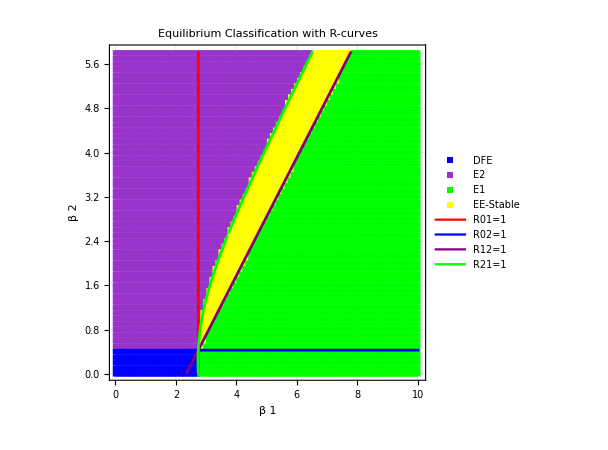

```mathematica
plotInd={1,2};varInd={1,2,3};p0val=par/.coP;steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[{fPl,unC,res}=scan[RHS,var,par,p0val,plotInd,varInd,Automatic,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]
fPl
```

```mathematica
Export["LiScan.pdf",fPl]
```

LiScan.pdf